## EJERCICIO 6 - Algoritmo de Gerla

## Alumnos: Rubén Ripa García Victor Hugo Contreras y Félix Sanz González Fecha: 05/12/2024

Aplicar el algoritmo de Gerla en la siguiente red donde los nodos vienen identificados mediante letras (A, B, C, D y E) y los enlaces mediante números (del 1 al 7). Para simplificar, los enlaces son unidireccionales.

-Graphics-

El tráfico de entrada consta únicamente de dos flujos que son: γ_AD = 2 paquetes/seg y γ_BE = 4 paquetes/seg. La longitud media de los paquetes es 1/μ’ = 1000 bits/paquete. Las capacidades de los enlaces son las siguientes (en bits/seg): C_1=C_3=C_6=5000 bps, C_2=C_4=C_5=C_7=10000 bps.

El vector de flujo inicial (f⃗)^(0) es igual a {2000, 0, 0, 4000, 0, 4000, 0}
El tráfico de AD va directamente de A a D y el tráfico de BE va de B a C y luego de C a E

```mathematica
Clear["Global`*"]
```

```mathematica
(* DATOS *)
γAD=2; (* Tráfico externo del flujo AD *)
γBE=4; (* Tráfico externo del flujo BE *)
μ=1/1000; (* Tasa de servicio (en paquetes/s) *)
l=1000; (* Valor medio de la longitud de los paquetes (en bits/paquete) *)
Nodos=5; (* Número de nodos *)
M=7; (* Número de enlaces *)

γjk={{0,0,0,2,0},{0,0,0,0,4},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}; (* Tráfico externo *)
γ=∑_(j=1)^Nodos ∑_(k=1)^Nodos γjk[[j]][[k]]; (* Tasa media total de paquetes externos (paq/seg) *)
Ci={5000,10000,5000,10000,10000,5000,10000}; (* Capacidad de los enlaces *)

λi={γAD,0,0,γBE,0,γBE,0}; (* Valor medio de la tasa de paquetes de los enlaces i (en paquetes/s) *)
```

```mathematica
Treal=∑_(i=1)^M 1/γ*λi[[i]]/(μ*Ci[[i]]-λi[[i]])//N
```

0.888889

## ITERACIÓN 1

## PASO 1

Tomar n = 0 -Graphics-

```mathematica
f0=λi/μ(* Vector de flujo inicial *)
```

{2000,0,0,4000,0,4000,0}

## PASO 2

Sensibilidad del retardo medio de tránsito al aumento en el flujo en dicho enlace     
Derivando parcialmente T respecto de f_i = λ_i / μ’ queda la siguiente fórmula -Graphics-

```mathematica
li=Ci/(γ*(Ci-f0)^2)
li//N
```

{1/10800,1/60000,1/30000,1/21600,1/60000,1/1200,1/60000}

{0.0000925926,0.0000166667,0.0000333333,0.0000462963,0.0000166667,0.000833333,0.0000166667}

## PASO 3

Calcular la tasa incremental de coste para el vector (f⃗)^(n) -Graphics-

```mathematica
β0=∑_(i=1)^M li[[i]]*f0[[i]]//N
```

3.7037

## PASO 4

Calcular las rutas más cortas entre cada par de nodos, utilizando como métrica la sensibilidad de los canales

```mathematica
(* Para el flujo AD, hay 3 posibilidades: AD, ACD, ABCD *)
liAD=li[[1]];
liACD=li[[2]]+li[[5]];
liABCD=li[[3]]+li[[4]]+li[[5]];
liFlujoAD={liAD,liACD,liABCD}//N
MinRutaAD=Min[liFlujoAD] (* La ruta más corta entre AD es la de ACD *)

(* Para el flujo BE, hay 2 posibilidades: BCE, BCDE *)
liBCE=li[[4]]+li[[6]];
liBCDE=li[[4]]+li[[5]]+li[[7]];
liFlujoBE={liBCE,liBCDE}//N
MinRutaBE=Min[liFlujoBE] (* La ruta más corta entre BE es la de BCDE *)
```

{0.0000925926,0.0000333333,0.0000962963}

0.0000333333

{0.00087963,0.0000796296}

0.0000796296

Calcular el vector de flujo resultante de utilizar las rutas más cortas. -Graphics-

```mathematica
λi={0,γAD,0,γBE,γAD+γBE,0,γBE};
ϕ=λi/μ
```

{0,2000,0,4000,6000,0,4000}

## PASO 5

Calcular la tasa incremental de coste para el flujo ϕ⃗ -Graphics-

```mathematica
b0=∑_(i=1)^M li[[i]]*ϕ[[i]]//N
```

0.385185

## PASO 6

Condición de parada del algoritmo:
  · Si β_n - b_n < ϵ donde ϵ > 0 → PARAR ((f⃗)^(n) es la solución)
  · Si no, ir al PASO 7

```mathematica
β0-b0
```

3.31852

Con este resultado, el valor de ϵ debería ser mayor a 3.31852 para que se cumpla la condición de parada del algoritmo, pero es bastante elevado. Por lo tanto, se va a realizar otra iteración para conseguir un valor de ϵ más pequeño y un resultado más preciso.

## PASO 7

Calcular α (0 ≤ α ≤ 1) tal que minimice T → -Graphics-

```mathematica
T[α_]=∑_(i=1)^M 1/γ*((1-α)*f0[[i]]+α*ϕ[[i]])/(Ci[[i]]-((1-α)*f0[[i]]+α*ϕ[[i]]));
```

```mathematica
(* FORMA 1: Derivando e igualando a cero para calcular los mínimos *)
dT=D[T[α],α];
αSol=NSolve[dT==0,α];
αMin=SelectFirst[α/. αSol,Element[#,Reals]&&0<=#<=1&]

(* FORMA 2: Obteniendo el valor de α que minimice el retardo medio T *)
αSol=NMinimize[{T[α],0<=α<=1},α,Method->"DifferentialEvolution",AccuracyGoal->10];
αMin=α/.αSol[[2]]
```

0.585623

0.585623

```mathematica
Treal0=T[αMin]//N
```

0.390255

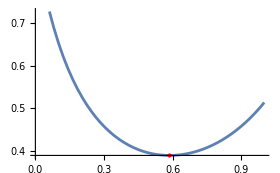

```mathematica
Plot[T[α],{α,0,1},Epilog->{Red,PointSize[Large],Point[{αMin,T[αMin]}]}]
```

## PASO 8

Desviación de flujo, donde el resultado de la asignación indica que parte del flujo es desviado por las rutas más cortas y el retardo medio de tránsito más bajo -Graphics-

```mathematica
f1=(1-αMin)*f0+αMin*ϕ
```

{828.754,1171.25,0.,4000.,3513.74,1657.51,2342.49}

## ITERACIÓN 2

## PASO 1

Tomar n = 1 -Graphics-

```mathematica
f1(* Vector de flujo 1 *)
```

{828.754,1171.25,0.,4000.,3513.74,1657.51,2342.49}

## PASO 2

Sensibilidad del retardo medio de tránsito al aumento en el flujo en dicho enlace     
Derivando parcialmente T respecto de f_i = λ_i / μ’ queda la siguiente fórmula -Graphics-

```mathematica
li=Ci/(γ*(Ci-f1)^2)
```

{0.0000478947,0.0000213821,0.0000333333,0.0000462963,0.000039615,0.0000745895,0.0000284233}

## PASO 3

Calcular la tasa incremental de coste para el vector (f⃗)^(n) -Graphics-

```mathematica
β1=∑_(i=1)^M li[[i]]*f1[[i]]
```

0.579333

## PASO 4

Calcular las rutas más cortas entre cada par de nodos, utilizando como métrica la sensibilidad de los canales

```mathematica
(* Para el flujo AD, hay 3 posibilidades: AD, ACD, ABCD *)
liAD=li[[1]];
liACD=li[[2]]+li[[5]];
liABCD=li[[3]]+li[[4]]+li[[5]];
liFlujoAD={liAD,liACD,liABCD}//N
MinRutaAD=Min[liFlujoAD] (* La ruta más corta entre AD es la de AD *)

(* Para el flujo BE, hay 2 posibilidades: BCE, BCDE *)
liBCE=li[[4]]+li[[6]];
liBCDE=li[[4]]+li[[5]]+li[[7]];
liFlujoBE={liBCE,liBCDE}//N
MinRutaBE=Min[liFlujoBE] (* La ruta más corta entre BE es la de BCDE *)
```

{0.0000478947,0.0000609971,0.000119245}

0.0000478947

{0.000120886,0.000114335}

0.000114335

Calcular el vector de flujo resultante de utilizar las rutas más cortas. -Graphics-

```mathematica
λi={γAD,0,0,γBE,γBE,0,γBE};
ϕ=λi/μ
```

{2000,0,0,4000,4000,0,4000}

## PASO 5

Calcular la tasa incremental de coste para el flujo ϕ⃗ -Graphics-

```mathematica
b1=∑_(i=1)^M li[[i]]*ϕ[[i]]//N
```

0.553128

## PASO 6

Condición de parada del algoritmo:
  · Si β_n - b_n < ϵ donde ϵ > 0 → PARAR ((f⃗)^(n) es la solución)
  · Si no, ir al PASO 7

```mathematica
β1-b1
```

0.0262049

Ahora, ya se ha obtenido un resultado .08muchísimo más pequeño en comparación con el de la primera iteración, por lo que en esta segunda iteración, el valor de ϵ debería ser mayor que 0.0262049 para que se cumpla la condición de parada del algoritmo. Este ya sería un resultado muy ACEPTABLE, pero se ha decidido realizar una última iteración.

## PASO 7

Calcular α (0 ≤ α ≤ 1) tal que minimice T → -Graphics-

```mathematica
T[α_]=∑_(i=1)^M (1/γ)*(((1-α)*f1[[i]]+α*ϕ[[i]])/(Ci[[i]]-((1-α)*f1[[i]]+α*ϕ[[i]])));
```

```mathematica
(* FORMA 1: Derivando e igualando a cero para calcular los mínimos *)
dT=D[T[α],α];
αSol=NSolve[dT==0,α];
αMin=SelectFirst[α/. αSol,Element[#,Reals]&&0<=#<=1&]

(* FORMA 2: Obteniendo el valor de α que minimice el retardo medio T *)
αSol=NMinimize[{T[α],0<=α<=1},α,Method->"DifferentialEvolution",AccuracyGoal->10];
αMin=α/.αSol[[2]]
```

0.150081

0.150081

```mathematica
Treal1=T[αMin]//N
```

0.388321

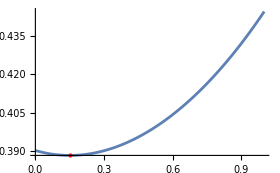

```mathematica
Plot[T[α],{α,0,1},Epilog->{Red,PointSize[Large],Point[{αMin,T[αMin]}]}]
```

## PASO 8

Desviación de flujo, donde el resultado de la asignación indica que parte del flujo es desviado por las rutas más cortas y el retardo medio de tránsito más bajo -Graphics-

```mathematica
f2=(1-αMin)*f1+αMin*ϕ
```

{1004.53,995.465,0.,4000.,3586.72,1408.75,2591.25}

## ITERACIÓN 3

## PASO 1

Tomar n = 2 -Graphics-

```mathematica
f2(* Vector de flujo 2 *)
```

{1004.53,995.465,0.,4000.,3586.72,1408.75,2591.25}

## PASO 2

Sensibilidad del retardo medio de tránsito al aumento en el flujo en dicho enlace     
Derivando parcialmente T respecto de f_i = λ_i / μ’ queda la siguiente fórmula -Graphics-

```mathematica
li=Ci/(γ*(Ci-f2)^2)
```

{0.0000522016,0.0000205554,0.0000333333,0.0000462963,0.0000405217,0.000064614,0.000030364}

## PASO 3

Calcular la tasa incremental de coste para el vector (f⃗)^(n) -Graphics-

```mathematica
β2=∑_(i=1)^M li[[i]]*f2[[i]]
```

0.573131

## PASO 4

Calcular las rutas más cortas entre cada par de nodos, utilizando como métrica la sensibilidad de los canales

```mathematica
(* Para el flujo AD, hay 3 posibilidades: AD, ACD, ABCD *)
liAD=li[[1]];
liACD=li[[2]]+li[[5]];
liABCD=li[[3]]+li[[4]]+li[[5]];
liFlujoAD={liAD,liACD,liABCD}//N
MinRutaAD=Min[liFlujoAD] (* La ruta más corta entre AD es la de AD *)

(* Para el flujo BE, hay 2 posibilidades: BCE, BCDE *)
liBCE=li[[4]]+li[[6]];
liBCDE=li[[4]]+li[[5]]+li[[7]];
liFlujoBE={liBCE,liBCDE}//N
MinRutaBE=Min[liFlujoBE] (* La ruta más corta entre BE es la de BCE *)
```

{0.0000522016,0.0000610771,0.000120151}

0.0000522016

{0.00011091,0.000117182}

0.00011091

Calcular el vector de flujo resultante de utilizar las rutas más cortas. -Graphics-

```mathematica
λi={γAD,0,0,γBE,0,γBE,0};
ϕ=λi/μ
```

{2000,0,0,4000,0,4000,0}

## PASO 5

Calcular la tasa incremental de coste para el flujo ϕ⃗ -Graphics-

```mathematica
b2=∑_(i=1)^M li[[i]]*ϕ[[i]]//N
```

0.548045

## PASO 6

Condición de parada del algoritmo:
  · Si β_n - b_n < ϵ donde ϵ > 0 → PARAR ((f⃗)^(n) es la solución)
  · Si no, ir al PASO 7

```mathematica
β2-b2
```

0.0250869

Por último, se puede comprobar que se ha obtenido un resultado similar al de la segunda iteración, pero ligeramente menor, por lo que ya si que se puede dar por bueno este resultado, con un ϵ que debería ser mayor a 0.0250869. La rutas más cortas y óptimos son:
  · Flujo γAD: Ruta óptima AD
  · Flujo γBE: Ruta óptima BCE
  
{1004.53, 995.465, 0., 4000., 3586.72, 1408.75, 2591.25}
{5000, 10000, 5000, 10000, 10000, 5000, 10000}

-Graphics--Graphics-

```mathematica
v1={1,0,0,1,0,1,0} (* AD y BCE *)
v2={1,0,0,1,1,0,1} (* AD y BCDE *)
v3={0,1,0,1,1,1,0} (* ACD y BCE *)
v4={0,1,0,1,1,0,1}(* ACD y BCDE *)
v5={0,0,1,1,1,1,0} (* ABCD y BCE *)
v6={0,0,1,1,1,0,1} (* ABCD y BCDE *)
```

{1,0,0,1,0,1,0}

{1,0,0,1,1,0,1}

{0,1,0,1,1,1,0}

{0,1,0,1,1,0,1}

{0,0,1,1,1,1,0}

{0,0,1,1,1,0,1}

## AUTOMATIZACIÓN DEL ALGORITMO GERLA EN MATHEMATICA

```mathematica
(*DATOS INICIALES*)

M = 7;

(*Longitud media de paquetes bit/pack*)
lonmedia=1000; 
mu = 1/lonmedia;

(*throught de nodos con trafico externo pack/seg*)
γad=2; γbe=4; 

(*matriz trafico de nodos de traFico externo*)
γjk={{0,0,0,2,0},{0,0,0,0,4},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}};

(*orden de canales={(1),(2},(3),(4),(5),(6),(7)*)
Ci={5000,10000,5000,10000,10000,5000,10000};

(*Tasa λi en paq/seg*)
λi={1*γad,0,0,1*γbe,0,1*γbe,0}
gamma=Total[Total[γjk]];
```

{2,0,0,4,0,4,0}

```mathematica
(*Funciones que son de utilidad a la hora de automatizar*)

obtenerIi [Ci_,γ_, vectorf0_] := Ci/(γ*(Ci-(vectorf0))^2)//N
obtenerB0[Ii_, vectorf0_]:=Total[Ii*vectorf0]
obtenerFlujoComp0[a_,vectorf0_,vectorFlujoResultante0_]:=(1-a)vectorf0+(a*vectorFlujoResultante0)
```

```mathematica
(*vector de flujo inicial (el que nos dan)*)

vectorf0=λi*lonmedia;
res = {0,0,0,0,0,0,0,0,0,0,0,0,0,vectorf0,0,0};
res[[14]]
```

{2000,0,0,4000,0,4000,0}

```mathematica
(*Función a iterar*)

funcionIterar[Ci_,gamma_,vectorf0_,mu_,M_,niteracion_]:=Module[{resultadoIter, a,b,Ii,B0,IiAD,menosSensibleGammaAD,IiBE,menosSensibleGammaBE, posMinimoAD, posMinimoBE, λi, ϕ, b0, dT, αSol, αMin, fnew},(*Cálculos dentro del módulo*)
(*Paso 2:*)
Ii=obtenerIi[Ci,gamma,vectorf0];

(*Paso 3:*)
B0=obtenerB0[Ii,vectorf0];


(*Paso 4:*)
IiAD={Ii[[1]],Ii[[2]]+Ii[[5]],Ii[[3]]+Ii[[4]]+Ii[[5]]}; (*El tráfico AD,con 3 opciones:AD,ACD,ABCD*)
menosSensibleGammaAD=Min[IiAD];
posMinimoAD = Flatten[Position[IiAD,menosSensibleGammaAD],2];
a = posMinimoAD[[1]];
(*El tráfico BE,con 2 opciones:BCE,BCDE*)
IiBE={Ii[[4]]+Ii[[6]],Ii[[4]]+Ii[[5]]+Ii[[7]]};
menosSensibleGammaBE=Min[IiBE];
posMinimoBE= Flatten[Position[IiBE,menosSensibleGammaBE],2];
b = posMinimoBE[[1]];

Switch[{a,b},
{1,1},λi={1*γad,0,0,1*γbe,0,1*γbe,0},
{1,2},λi={1*γad,0,0,1*γbe,1*γbe,0,1*γbe},
{2,1},λi={0,1*γad,0,1*γbe,1*γad,1*γbe,0},
{2,2},λi={0,1*γad,0,1*γbe,(1*γad)+(1*γbe),0,1*γbe},
{3,1},λi={0,0,1*γad,(1*γad)+(1*γbe),1*γad,1*γbe,0},
{3,2},λi={0,0,1*γad,(1*γad)+(1*γbe),(1*γad) +(1*γbe) ,0,1*γbe},
{_,_},"Valores no especificados"];

ϕ=λi/mu;

(*Paso 5:*)
b0 = obtenerB0[Ii,ϕ];

(*Paso 6:*)
resultadoIter = B0-b0;

(*Paso 7:*)
obtenerT0[α_]=∑_(i=1)^M 1/gamma*((1-α)*vectorf0[[i]]+α*ϕ[[i]])/(Ci[[i]]-((1-α)*vectorf0[[i]]+α*ϕ[[i]]));
(*αSol=NMinimize[{obtenerT0[α_],0<=α<=1},α,Method->"DifferentialEvolution",AccuracyGoal->10];
αMin=α/.αSol[[2]];
Plot[obtenerT0[α],{α,0,1},Epilog->{Red,PointSize[Large],Point[{αMin,obtenerT0[αMin]}]}];*)

dT=D[obtenerT0[α],α];
αSol=NSolve[dT==0,α];
αMin=SelectFirst[α/. αSol,Element[#,Reals]&&0<=#<=1&];

(*Paso 8:*)
fnew=(1-αMin)*vectorf0+αMin*ϕ;


(*Mostrar las variables por pantalla*)
Print["\n"];
	Print[" --------------- N.ba ITERACION = ", niteracion , " --------------------------------"];
Print["Ii: ",Ii];
Print["B0: ",B0];
Print["IiAD: ",IiAD];
Print["Menos sensible GammaAD: ",menosSensibleGammaAD, posMinimoAD];
Print["IiBE: ",IiBE];
Print["Menos sensible GammaBE: ",menosSensibleGammaBE, posMinimoBE];
Print["a = " ,a];
Print["b = " ,b];
Print["λi = ",λi];
Print["ϕ = ",ϕ];
Print["b0 = ",b0];
Print["resultadoIter = ", resultadoIter];
Print["αMin = ", αMin];
Print["fnew = ",fnew ];
(*devolvemos todas las variables como una lista*)
res = {Ii,B0,IiAD,menosSensibleGammaAD,IiBE,menosSensibleGammaBE, posMinimoAD,posMinimoBE,λi,ϕ,b0, resultadoIter, αMin, fnew, niteracion}]
```

```mathematica
(*Implementación: se itera hasta obtener un valor de resultadoIter < EpsilonMax y se muestran los resultados parciales por cada iteración*)

epsilonmax = 0.024;
niteracion = 0;

(*vector de flujo inicial (el que nos dan)*)
vectorf0=λi*lonmedia;
res = {0,0,0,0,0,0,0,0,0,0,0,100000,0,vectorf0,0,0}; (*Cargamos un valor de resultadoIter muy alto para forzar la ejecucion del while al menos una vez*)

While[res[[12]]> epsilonmax, (*Comparamos resultadoIter con EpsilonMax para saber si hemos cumplido con el criterio*)
res  = funcionIterar[Ci,gamma,res[[14]],mu,M,niteracion];
niteracion++;
]
```

--------------- N.ba ITERACION = 0 --------------------------------

Ii: {0.0000925926,0.0000166667,0.0000333333,0.0000462963,0.0000166667,0.000833333,0.0000166667}

B0: 3.7037

IiAD: {0.0000925926,0.0000333333,0.0000962963}

Menos sensible GammaAD: 0.0000333333{2}

IiBE: {0.00087963,0.0000796296}

Menos sensible GammaBE: 0.0000796296{2}

a = 2

b = 2

λi = {0,2,0,4,6,0,4}

ϕ = {0,2000,0,4000,6000,0,4000}

b0 = 0.385185

resultadoIter = 3.31852

αMin = 0.585623

fnew = {828.754,1171.25,0.,4000.,3513.74,1657.51,2342.49}

--------------- N.ba ITERACION = 1 --------------------------------

Ii: {0.0000478947,0.0000213821,0.0000333333,0.0000462963,0.000039615,0.0000745895,0.0000284233}

B0: 0.579333

IiAD: {0.0000478947,0.0000609971,0.000119245}

Menos sensible GammaAD: 0.0000478947{1}

IiBE: {0.000120886,0.000114335}

Menos sensible GammaBE: 0.000114335{2}

a = 1

b = 2

λi = {2,0,0,4,4,0,4}

ϕ = {2000,0,0,4000,4000,0,4000}

b0 = 0.553128

resultadoIter = 0.0262049

αMin = 0.150081

fnew = {1004.53,995.465,0.,4000.,3586.72,1408.75,2591.25}

--------------- N.ba ITERACION = 2 --------------------------------

Ii: {0.0000522016,0.0000205554,0.0000333333,0.0000462963,0.0000405217,0.000064614,0.000030364}

B0: 0.573131

IiAD: {0.0000522016,0.0000610771,0.000120151}

Menos sensible GammaAD: 0.0000522016{1}

IiBE: {0.00011091,0.000117182}

Menos sensible GammaBE: 0.00011091{1}

a = 1

b = 1

λi = {2,0,0,4,0,4,0}

ϕ = {2000,0,0,4000,0,4000,0}

b0 = 0.548045

resultadoIter = 0.0250869

αMin = 0.0505854

fnew = {1054.89,945.109,0.,4000.,3405.28,1539.83,2460.17}

--------------- N.ba ITERACION = 3 --------------------------------

Ii: {0.0000535428,0.0000203274,0.0000333333,0.0000462963,0.0000383227,0.0000696022,0.0000293174}

B0: 0.57068

IiAD: {0.0000535428,0.0000586501,0.000117952}

Menos sensible GammaAD: 0.0000535428{1}

IiBE: {0.000115899,0.000113936}

Menos sensible GammaBE: 0.000113936{2}

a = 1

b = 2

λi = {2,0,0,4,4,0,4}

ϕ = {2000,0,0,4000,4000,0,4000}

b0 = 0.562831

resultadoIter = 0.00784828

αMin = 0.0546464

fnew = {1106.54,893.462,0.,4000.,3437.78,1455.68,2544.32}